# Ben’s Mathematica Trivia

## Variable Naming

Sometimes, i want to name variables using subscripts. Mathematica treats these variables as lesser symbols, however. Note that:

```mathematica
Subscript[a, 1]={1, 2};
Subscript[a, 2]={3, 4};
a= 6;
```

```mathematica
Subscript[a, 1]
```

6_1

Gives unexpected results. Instead, in the local notebook (this doesn’t carry across concurrently-open notebooks like most other things do), include the following two lines:

```mathematica
Needs["Notation`"];
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]
```

Now, the same code behaves differently:

```mathematica
Subscript[a, 1]={1, 2};
Subscript[a, 2]={3, 4};
a= 6;
```

```mathematica
Subscript[a, 1]
```

{1,2}

Note that this does NOT work for superscripts (no idea why!). Source: http://stackoverflow.com/questions/5481216/subscripted-variables

This is till hokey. Even with this mod, if you have a variable the same name as a subscript sometimes the subscripted variable ceases to be a symbol.

## Rules and Replacements

Substitute a value for x in an expression:

```mathematica
x+1/.x->3
```

4

WARNING: I’ve been bitten by Mathematica’s intelligence here. Say I have a vector equation, and I want to substitue a vector quantity:

```mathematica
x+{1,1,1}/.x->{2,2,2}
```

{{3,3,3},{3,3,3},{3,3,3}}

That ought to have produced just a single {3,3,3}, right? Wrong! It turns out Mathematica trys to save us time by automatically expanding scalars in vector equations. That’s handy, for example, when I want to do

```mathematica
{1,1,1}+2
```

{3,3,3}

It sees the 2 as a scalar and automatically changes it to {2,2,2} for the vector add. BUT, in the above example, it thought x was a scalar, so before applying the rule, it change the expression to {x,x,x}+{1,1,1}, so x gets replaced 3 times! We can verify the rule has been executed three times using a delayed rule:

```mathematica
x+{1,1,1}/.x:>{RandomInteger[{0,100}],2,2}
```

{{4,3,3},{11,3,3},{68,3,3}}

## Plotting

Text on plots, matrix of plots, styles:

```mathematica
styles=Flatten[Table[{Directive[color,Thick],Directive[Dashed,color,Thick],Directive[Dotted,color,Thick]},{color,{Black,Gray}}]];
```

```mathematica
k=0.1;
```

```mathematica
u1[x_,t_]:=k Cos[π c t] Sin[π x] - k/2 Cos[π 2 c t] Sin[2 π x]/.c->1;
```

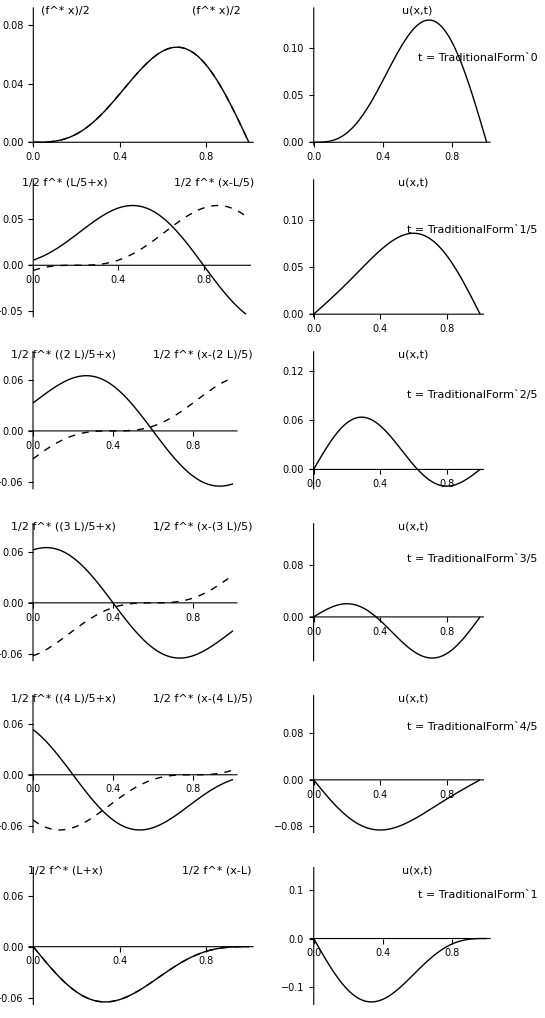

```mathematica
GraphicsGrid[Table[{Show[{Plot[{1/2 fstar1[x+c t]/.{c->1},1/2 fstar1[x-c t]/.{c->1}},{x,0,1},ImageSize->250,PlotRange->{0.14,-0.08},PlotStyle->styles],Graphics[Text[1/2 SuperStar[f](x+L*t),{0.15,0.09}]],Graphics[Text[1/2 SuperStar[f](x-L*t),{0.85,0.09}]]}], Show[{Plot[u1[x,t],{x,0,1},PlotRange->{0.15,-0.15},PlotStyle->{Black,Thick},ImageSize->250],Graphics[Text[StringForm["t = ``",t],{0.95,0.09}]],Graphics[Text["u(x,t)",{0.6,0.14}]]}]},{t,0,1,1/5}]]
```

Putting graphic side by side

```mathematica
GraphicsRow[{Plot[],Plot[]}]
```

Why don’t legends work the way they’re supposed to?

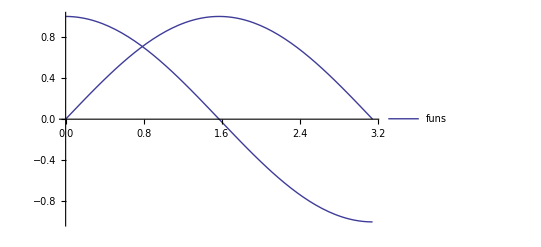

```mathematica
funs:={Sin[x], Cos[x]};
Plot[funs,{x,0,π},PlotLegends->"Expressions"]
```

See http://stackoverflow.com/questions/11940444/plotlegend-in-mathematica-does-not-work-for-a-table-of-functions for the details, but we need to evaluate the list before plugging it into Plot so it detects the multiple traces.

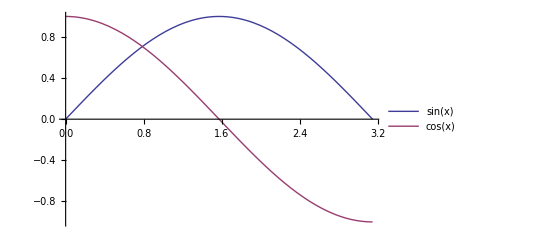

```mathematica
Plot[Evaluate@funs,{x,0,π},PlotLegends->"Expressions"]
```

Plotting with continuous and discrete line types (and legends that work)

The trick to keeping PlotMarkers from showing up on the line intended to be continuous is to use PlotMarkers and pass “” (empty string). Not sure how to get the others to be automatic yet, however. Note that to get the symbols and the lines in the legend, you need to use PlotLegends->PointLegend and pass the option Joined->Automatic.

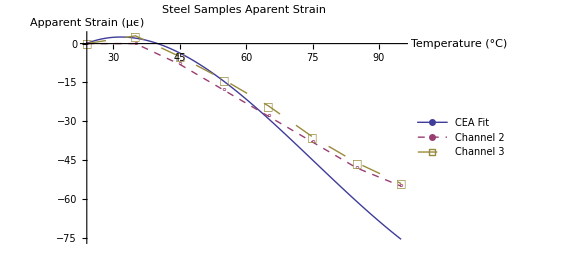

```mathematica
ListPlot[data,
Joined->True,PlotMarkers->{"","∘","□"},PlotStyle->{Thick,Directive[Dashed, PointSize[Large]],Directive[Dashing[Large]]},PlotLegends->PointLegend[{"CEA Fit","Channel 2", "Channel 3"},Joined->Automatic],
AxesLabel->{"Temperature (°C)","Apparent Strain (μϵ)"},PlotLabel->"Steel Samples Aparent Strain"]
```

## Grids and Tables

```mathematica
Grid[{{"Method","RMS y_1-y_1^*","RMS y_2-y_2^*"},{"h = "<>ToString[hs[[1]]]<>" Explicit",N[experr[[1,1,1]],4],N[experr[[1,2,1]],4]},
{"h = "<>ToString[hs[[1]]]<>" Implicit",N[imperr[[1,1,1]],4],N[imperr[[1,2,1]],4]},
{"h = "<>ToString[hs[[2]]]<>" Explicit",N[experr[[2,1,1]],4],N[experr[[2,2,1]],4]},
{"h = "<>ToString[hs[[2]]]<>" Implicit",N[imperr[[2,1,1]],4],N[imperr[[2,2,1]],4]},
{"h = "<>ToString[hs[[3]]]<>" Explicit",N[experr[[3,1,1]],4],N[experr[[3,2,1]],4]},
{"h = "<>ToString[hs[[3]]]<>" Implicit",N[imperr[[3,1,1]],4],N[imperr[[3,2,1]],4]}

},Dividers->{False,{{False,True}}}]
```

Method | RMS y_1-y_1^* | RMS y_2-y_2^*
h = 0.1 Explicit | 1.73032×10^94 | 1.72859×10^97
h = 0.1 Implicit | 0.0108284 | 0.00280056
h = 0.01 Explicit | 1.323×10^472 | 1.322×10^475
h = 0.01 Implicit | 0.00111102 | 0.00816092
h = 0.0001 Explicit | 0.0000111669 | 0.000728849
h = 0.0001 Implicit | 0.000559179 | 0.000687468

## Functions and Manipulations

Function application to a large dataset

```mathematica
fix[x_]:=If[x<0,x-2,x];
```

```mathematica
list={1,2,-3,4};
```

```mathematica
fix/@list
```

{1,2,-5,4}

Setting functions to use specific types for their arguments:

Check that the argument is a list:

```mathematica
f[x_?ListQ]=x+1;
```

Check that the argument is a list of numbers only (from http://stackoverflow.com/questions/8786389/what-is-the-recommended-way-to-check-that-a-list-is-a-list-of-numbers-in-argumen)

```mathematica
f[x_/;VectorQ[x,NumericQ]] = x+1;
```

Alternately, we can use __, which means “one or more of”:

```mathematica
f[x_/;MatchQ[x,{__Integer}]]=x+1;
```

Note that this is much faster than {__?NumericQ}, but there isn’t an equivalent (that I’ve found) for the syntax above which works for any number; just Integer, String, etc.

Additionally test whether the numeric quantities in the list are real:

```mathematica
f[x_/;VectorQ[x,NumericQ]&&Re[x]==x]=x+1;
```

For code where performance is important, you can define complex criteria for testing, then disable for inner functions after the code is finished:

```mathematica
pattNumericList=_?(VectorQ[#,NumericQ]&);
f[x:pattNumericList]=x+1;
```

Then, to turn off the pattern check, define pattNumericList = _. NOTE: in the expression for pattNumericList, the internal function & goes INSIDE the last ), or it doesn’t work.

Design patterns:

```mathematica
pattTensor2=_?(MatrixQ[#,NumericQ]&&Dimensions[#]=={2,2}&);
```

## Text and Strings

printf() equivalent:

```mathematica
fish = StringForm["This is my text = ``, and I like ``",23.4/4,"fish"]
```

This is my text = 5.85, and I like fish

However, this has two difficulties. StringForm works great for displaying text on the screen, but what we produced was not truly text:

```mathematica
Head[fish]
```

StringForm

What we really have is a StringForm object. To get it into a string, we need to do ToString:

```mathematica
fishstr = ToString[fish]
Head[fishstr]
```

This is my text = 5.85, and I like fish

String

Also, most of the formatting options we’re used to with C/Matlab printf aren’t present. A few workarounds:

```mathematica
(*%.4f equivalent *)
ToString[StringForm["The part is `` in. long.",Round[1.2345678,0.0001]]]
```

The part is 1.2346 in. long.

```mathematica
(*%5i leading zeros, fixed total width equivalent*)
ToString[StringForm["N`` G01 X1. Y1. Z1.\n", StringJoin[ToString/@PadLeft[IntegerDigits[100],5]]]]
```

N00100 G01 X1. Y1. Z1.

Concatinating Strings
To concatinate strings (make sure they’re really strings!), use the <> operator or StringJoin function.

```mathematica
fishstr <> ". Fish are cool"
StringJoin[ToString/@Table[i,{i,1,10}]]
```

This is my text = 5.85, and I like fish. Fish are cool

12345678910

## List Manipulations

```mathematica
list = {{1,2,3},{4,5,6},{7,8,9}};
```

Randomizing the order of the elements. This is hidden in the RandomSample documentation; the function doesn’t look like it does this with only one argument!

```mathematica
RandomSample[list]
```

{{7,8,9},{4,5,6},{1,2,3}}

Locating all the elements that match a rule:

```mathematica
Position[list, 3]
```

{{1,3}}

What if we want to locate all the elements that follow some criteria (say, x > 5)

```mathematica
Position[list,x_/;x>5]
```

{{2,3},{3,1},{3,2},{3,3}}

Extracting a series of list elements given a list of indexes

```mathematica
idxs = {{1,1},{3,3},{2,1}};
Extract[list, idxs]
```

{1,9,4}

What if we have the index we want to manipulate as a list, and want to replace just that element with a new value? Note that this does not update list; we would need to use list = ReplacePart...

```mathematica
idx={1,2};
ReplacePart[list,idx->4]
```

{{1,4,3},{4,5,6},{7,8,9}}

But that’s a lot of copying! What if I want to just assign that part? Not sure this is the correct way to do this, but this requires “0” time in Mathematica, whereas the above scales with the size of the object list.

```mathematica
Part[list,Sequence@@idx]=4;
list
```

{{1,4,3},{4,5,6},{7,8,9}}

What if I have a list of positions that all need to be updated? This will set them all to 42, but we have the index of the current entry (#), so we could do something more interesting. This shows up in my Octree implementation for distance field computation (skeletonization project)

```mathematica
Set[Part[list,Sequence@@#],42]&/@idxs;
list
```

{{42,4,3},{42,5,6},{7,8,42}}

Find which of a list of candidate indices has a certain value in the list:

```mathematica
interesting=Position[Extract[list,idxs],1]
```

{{1}}

A much more esoteric way to accomplish the same thing, without any particular benefit...

```mathematica
Position[idxs,_?(Extract[list,#]==1&),{1},Heads->False]
```

{{1}}

Note on the above, we have to specify level {1} only, or else it tries, successively, every layer of the list in turn, and we have to turn of checking Heads, or it trys to evaluate Extract[list, List] == 1, which throws an error. Note that Extract[list,#]==1 is about twice as fast as list[[Sequence@@#]==1 in my tests with 3D sparse arrays.

Sometimes, I want to find the minimum entry in a list, based on a single element of each item in the list. For example, in OctreeSDF, I call a function which returns a list of {distance, grad1, grad2, grad3}, and I want to take the entry with the smallest distance, but not throw away the associated other elements. I found a few ways to do this, and as usual, patterns are the best way, approaching the speed of a straight Min.

```mathematica
list={{1,a,b},{4,c,d},{2,e,f},{-1,a,c}};
Timing[Table[Min[list[[;;,1]]],{i,1,10000}][[1]]]
Timing[Table[TakeSmallestBy[list,First,1],{i,1,10000}][[1]]]
Timing[Table[MinimalBy[list,First,1],{i,1,10000}][[1]]]
Timing[Table[SelectFirst[list,First[#]==Min[list[[;;,1]]]&],{i,1,10000}][[1]]]
Timing[Table[FirstCase[list, x_/;(x[[1]]==Min[list[[;;,1]]])],{i,1,10000}][[1]]]
Timing[Table[FirstCase[list,{Min[list[[;;,1]]],_,_}],{i,1,10000}][[1]]]
```

{0.0156001,-1}

{0.109201,{{-1,a,c}}}

{0.561604,{{-1,a,c}}}

{0.109201,{-1,a,c}}

{0.124801,{-1,a,c}}

{0.0468003,{-1,a,c}}

#### SparseArrays

Sparse Arrays do not play well with Cases (it expands the sparse array), and I can’t get Position to work at all. Instead, use ArrayRules[] to get the contents of the sparse array, then use patterns on that to get what you want.

It is much, much faster go generate a long list of rules and then create a sparse array than to repeatedly do ReplaceParts to populate a big array. Note that if you’re generating it in a recursive manner, Sow and Reap are an order of magnitude or more faster than having a global variable you Join[] new entries to on every evaluation.

## Overriding Subscript

Subscript has no intrinsic assignment in mathematica. We can assign functions to specific subscripts:

```mathematica
Subscript[T_, xx]:=T[[1,1]]
Subscript[T_, yy]:=T[[2,2]]
Subscript[T_, xy]:=T[[1,2]]
```

```mathematica
Subscript[{{a, b},{c, d}}, xx]
```

a

We can also override the whole subscript operation with a specific function

```mathematica
Subscript[a_, b_]:=a+b
```

```mathematica
Subscript[25, c]
```

25+c

## Heads and Manipulating Heads

Drop a list into a function as if it were a list of arguments: Apply or @@

```mathematica
args={1,2,3};
f[a_,b_,c_]:=a+b+c
f@@args
```

6

## Advanced Stuff...

### Customizing key bindings

Keybindings are stored in ProgramFiles/Wolfram/Mathematica/<version>/SystemFiles/FrontEnd/TextResources/Windows/KeyEventTranslations.tr
Some people say you can make a copy of this in your user directory, but I haven’t had any luck. Following 
http://stackoverflow.com/questions/7327411/is-there-a-way-around-using-and-for-part-in-mathematica/7328495
I added the following customization on my system to automatically generate matching brackets, braces, and double brackets

Note: Mathemtaica automatically replaces the DoubleBracket calls in the text below. So copy and paste the following and then remove the ***’s (3 places).

(*Ben’s custom key bindings*)
Item[KeyEvent[“]”, Modifiers -> {Control}],
        FrontEndExecute[{
            FrontEnd`NotebookWrite[FrontEnd`InputNotebook[],
                “\[Right***DoubleBracket]”, After]
        }]], 
Item[KeyEvent[“[“, Modifiers -> {Control}],
        FrontEndExecute[{
            FrontEnd`NotebookWrite[FrontEnd`InputNotebook[],
                “\[Left***DoubleBracket]”, After],
            FrontEnd`NotebookWrite[FrontEnd`InputNotebook[],
                “\[Right***DoubleBracket]”, Before]
        }]],  
Item[KeyEvent[“[“, Modifiers -> {Shift}],
        FrontEndExecute[{
            FrontEnd`NotebookWrite[FrontEnd`InputNotebook[],
                “{“, After],
            FrontEnd`NotebookWrite[FrontEnd`InputNotebook[],
                “}”, Before]
        }]], 
Item[KeyEvent[“[“],
        FrontEndExecute[{
            FrontEnd`NotebookWrite[FrontEnd`InputNotebook[],
                “[“, After],
            FrontEnd`NotebookWrite[FrontEnd`InputNotebook[],
                “]”, Before]
        }]],

### step[] - execute one step of the evaluation of an expression

This from http://mathematica.stackexchange.com/questions/334/how-do-i-evaluate-only-one-step-of-an-expression

```mathematica
SetAttributes[step,HoldAll]

step[expr_]:=Module[{P},P=(P=Return[#,TraceScan]&)&;
TraceScan[P,expr,TraceDepth->1]]
```

```mathematica
step[2+26*N[Sin[3]]-Cos[2.]]
```

2+3.66912+0.416147

### Furhter Reading

http://www.verbeia.com/mathematica/tips/Tricks.html